```mathematica
Clear["Global`*"];
$Version
```

13.3.1 for Microsoft Windows (64-bit) (July 24, 2023)

```mathematica
dropPath=Take[(FileNameSplit /@ # ) //Transpose,-1][[1]]&;
```

```mathematica
SetDirectory[NotebookDirectory[]];
here=NotebookDirectory[];
FileNames["*",here] //dropPath
```

{CTEQNNLO PDF Gen.nb,JAM22 PDF Gen.nb,JAM22 PPDF Gen.nb,LHAPDF,MP_packages,PDFdata50.csv,PPDFdata50.csv}

```mathematica
dirFilesLHA="./LHAPDF";
dirList=FileNames["*",dirFilesLHA];
```

```mathematica
dirPackages=here<>"MP_packages";
Get[dirPackages<>"/pdfParseLHA.m"];
Get[dirPackages<>"/pdfParseCTEQ.m"];
Get[dirPackages<>"/pdfErrors.m"];
```

Version: pdfCalc 5.0

Version: ManeParse 5.0: April 2021

- Required Package: pdfCalc --Loaded -

===============================================================

- pdfParseLHA -

Version:  5.0: April 2021

Authors: E.J. Godat, D.B. Clark & F.I. Olness

Please cite: **************

http://ncteq.hepforge.org/code/pdf.html

For a list of available commands, enter: ?pdf*

===============================================================

===============================================================

- pdfParseCTEQ -

Version:  5.0:  April 2021

Authors: D.B. Clark, E.J. Godat & F.I. Olness

Please cite: **************

http://ncteq.hepforge.org/code/pdf.html

For a list of available commands, enter: ?pdf*

===============================================================

===============================================================

- pdfErrors -

Version:  5.0; April 2021

Authors: D.B. Clark, E.J. Godat & F.I. Olness

Please cite: **************

http://ncteq.hepforge.org/code/pdf.html

For a list of available commands, enter: ?pdf*

===============================================================

```mathematica
CTEQ18NNLOList=Select[ FileNames["CT18NNLO",dirFilesLHA],DirectoryQ]
JAM22PDFNLOList=Select[ FileNames["JAM22-PDF_proton_nlo_pos_gluon",dirFilesLHA],DirectoryQ]
JAM22PPDFNLOList=Select[ FileNames["JAM22-PPDF_proton_nlo_pos_gluon",dirFilesLHA],DirectoryQ]
```

{./LHAPDF\CT18NNLO}

{./LHAPDF\JAM22-PDF_proton_nlo_pos_gluon}

{./LHAPDF\JAM22-PPDF_proton_nlo_pos_gluon}

```mathematica
pdfReset[]
pdfFamilyParseLHA[ JAM22PDFNLOList[[1]]] ;
```

Default Mathematica interpolator will be used.

All internal variables have been reset.

Syntax::com: 警告：在没有相邻表达式的情况下，碰到了逗号. 表达式将视为 Null 处理. 
.

Successfully read .\LHAPDF\JAM22-PDF_proton_nlo_pos_gluon\JAM22-PDF_proton_nlo_pos_gluon.info.

Included 979 files in the PDF family.

```mathematica
JAM22PDFNLOLen = Length[FileNames["JAM22-PDF_proton_nlo_pos_gluon*",JAM22PDFNLOList] ]-1
JAM22PDFNLOl = Range[1,JAM22PDFNLOLen];
```

979

```mathematica
pdfJAM22PDFNLOCentral[x__]:=pdfFunction[1,x]
SetAttributes[{pdfJAM22PDFNLOCentral},Listable]
```

```mathematica
pdfJAM22PDFNLOErr[x__]:=pdfMCError[JAM22PDFNLOl,x]
SetAttributes[{pdfJAM22PDFNLOErr},Listable]
```

## Test with PDFs

```mathematica
testflavor=0;
testq=2;
```

```mathematica
pdfJAM22PDFNLOCentral[testflavor,0.1,testq]
```

13.8472

```mathematica
pdfJAM22PDFNLOErr[testflavor,0.1,testq]
```

0.404169

```mathematica
NIntegrate[x*pdfJAM22PDFNLOCentral[0,x,3.097/2],{x,0,1}]
NIntegrate[x*pdfJAM22PDFNLOCentral[1,x,3.097/2],{x,0,1}]
NIntegrate[x*pdfJAM22PDFNLOCentral[2,x,3.097/2],{x,0,1}]
NIntegrate[x*pdfJAM22PDFNLOCentral[3,x,3.097/2],{x,0,1}]
NIntegrate[x*pdfJAM22PDFNLOCentral[4,x,3.097/2],{x,0,1}]
%+%%+%%%+%%%%+%%%%%
NIntegrate[x*pdfJAM22PDFNLOCentral[-1,x,3.097/2],{x,0,1}]
NIntegrate[x*pdfJAM22PDFNLOCentral[-2,x,3.097/2],{x,0,1}]
NIntegrate[x*pdfJAM22PDFNLOCentral[-3,x,3.097/2],{x,0,1}]
NIntegrate[x*pdfJAM22PDFNLOCentral[-4,x,3.097/2],{x,0,1}]
%+%%+%%%+%%%%+%%%%%
```

0.383934

0.176349

0.347036

0.00682503

0.0019813

0.916125

0.0380235

0.0294094

0.0131425

0.0019813

0.998681

```mathematica
Table[{x,x*pdfJAM22PDFNLOCentral[testflavor,x,testq]},{x,0.0001,0.001,0.0001}]
```

{{0.0001,4.53949},{0.0002,4.17112},{0.0003,3.98346},{0.0004,3.8632},{0.0005,3.7782},{0.0006,3.71413},{0.0007,3.66404},{0.0008,3.62418},{0.0009,3.59103},{0.001,3.56388}}

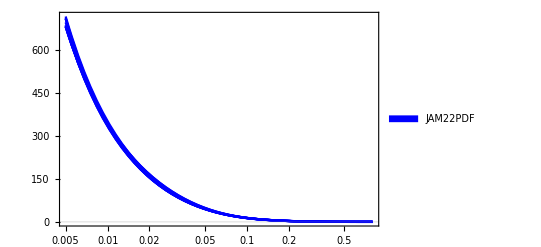

```mathematica
pltJAM22=Legended[Show[LogLinearPlot[pdfFunction[#,testflavor,x,testq],{x,0.005,0.8},PlotTheme-> "Scientific",PlotRange->All,PlotStyle->Blue] & /@Range[1,10]],Placed[SwatchLegend[{Blue},{"JAM22PDF"}],{0.8,0.5}]]
```

## Generating PDFs

```mathematica
QRef = 2;
dfl=1;
ufl =2;
gfl =21;
logrange = Table[Exp[logx],{logx,Log[0.0005],Log[0.6],Log[1200]/60}];
```

```mathematica
uquark=ParallelTable[{x,0,QRef,pdfJAM22PDFNLOCentral[ufl,x,QRef],pdfJAM22PDFNLOErr[ufl,x,QRef],0,"u"},{x,logrange}];
uantiquark=ParallelTable[{-x,0,QRef,-pdfJAM22PDFNLOCentral[-ufl,x,QRef],pdfJAM22PDFNLOErr[-ufl,x,QRef],0,"u"},{x,logrange}];
u = uquark~Join~uantiquark;
dquark=ParallelTable[{x,0,QRef,pdfJAM22PDFNLOCentral[dfl,x,QRef],pdfJAM22PDFNLOErr[dfl,x,QRef],0,"d"},{x,logrange}];
dantiquark=ParallelTable[{-x,0,QRef,-pdfJAM22PDFNLOCentral[-dfl,x,QRef],pdfJAM22PDFNLOErr[-dfl,x,QRef],0,"d"},{x,logrange}];
d = dquark~Join~dantiquark;
xg =ParallelTable[{x,0,QRef,x*pdfJAM22PDFNLOCentral[gfl,x,QRef],x*pdfJAM22PDFNLOErr[gfl,x,QRef],0,"g"},{x,logrange}];
PDFlst = u~Join~d~Join~xg;
```

```mathematica
headers={"x","t","mu","f","delta f","GPD type","flavor"};
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["PDFdata60.csv",Prepend[PDFlst,headers]];
```

C:\Users\Yuxun\Documents\Workspace\Github\GUMP_Data_Collection\Raw_Data\PDF_Fit

## Generating valance and sea PDFs (Not in use)

```mathematica
dVunp=ParallelTable[{x,Around[pdfJAM22PDFNLOCentral[dfl,x,testq]-pdfJAM22PDFNLOCentral[-dfl,x,testq],Sqrt[pdfJAM22UnpErr[dfl,x,testq]^2+pdfJAM22UnpErr[-dfl,x,testq]^2]]},{x,logrange}];

uVunp=ParallelTable[{x,Around[pdfJAM22PDFNLOCentral[ufl,x,testq]-pdfJAM22PDFNLOCentral[-ufl,x,testq],Sqrt[pdfJAM22UnpErr[ufl,x,testq]^2+pdfJAM22UnpErr[-ufl,x,testq]^2]]},{x,logrange}];

dbarfl=-1;
dbarunp=ParallelTable[{x,Around[pdfJAM22PDFNLOCentral[dbarfl,x,testq],pdfJAM22PDFNLOCentral[dbarfl,x,testq]]},{x,logrange}];
ubarfl =-2;
ubarunp=ParallelTable[{x,Around[pdfJAM22PDFNLOCentral[ubarfl,x,testq],pdfJAM22UnpErr[ubarfl,x,testq]]},{x,logrange}];xgunp=ParallelTable[{x,x*Around[pdfJAM22PDFNLOCentral[gfl,x,testq],pdfJAM22UnpErr[gfl,x,testq]]},{x,logrange}];
```

DumpGet::noopen: 无法打开 C:\Program Files\Wolfram Research\Mathematica\13.0\SystemFiles\Kernel\SystemResources\64Bit\Language\Uncertainty.mx.

General::sysfile: 通过符号 Around 对程序包 Language`Uncertainty` 进行二进制文件加载失败.

```mathematica
ListLogLinearPlot[{dVunp,uVunp},PlotTheme->"Scientific",PlotStyle->{Blue,Red},PlotRange->All,ImageSize->Scaled[0.2],PlotLegends->Placed[PointLegend[{Blue,Red},{"(q^V)_d(x)","(q^V)_u(x)"}],{0.8,0.8}]]
```

ListLogLinearPlot[{ParallelTable[{x,Uncertainty`CanonicalizeAround[Around[-pdfFunction[76,-1,x,2]+pdfFunction[76,1,x,2],√(1/554 ((pdfFunction[77,-1,x,2]+1/554 (1))^2+(pdfFunction[78,-1,x,2]+1/554 (1))^2+(pdfFunction[79,-1,x,2]+1/554 (1))^2+(pdfFunction[80,-1,x,2]+1/554 (1))^2+(pdfFunction[81,2,2]+1)^2+(1)^2+542+1^2+(1+1)^2+(pdfFunction[627,-1,x,2]+1/554 (1))^2+(pdfFunction[628,-1,x,2]+1/554 (1))^2+(pdfFunction[629,-1,x,2]+1/554 (1))^2+(1/554 (1)+pdfFunction[630,-1,x,2])^2)+1)]]},{x,{1}}],ParallelTable[1]},4,1]
 |  |  |  |

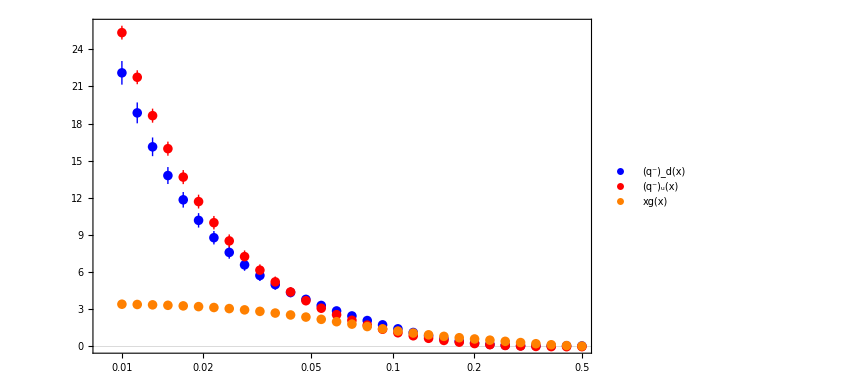

```mathematica
ListLogLinearPlot[{dbarunp,ubarunp,gunp},PlotTheme->"Scientific",PlotStyle->{Blue,Red,Orange},PlotRange->All,ImageSize->Scaled[0.2],PlotLegends->Placed[PointLegend[{Blue,Red,Orange},{"(q^-)_d(x)","(q^-)_u(x)","xg(x)"}],{0.8,0.8}]]
```

```mathematica
dfl=1;
dVpol=ParallelTable[{x,Around[pdfJAM22PolCentral[dfl,x,testq]-pdfJAM22PolCentral[-dfl,x,testq],Sqrt[pdfJAM22PolErr[dfl,x,testq]^2+pdfJAM22PolErr[-dfl,x,testq]]]},{x,logrange}];
ufl =2;
uVpol=ParallelTable[{x,Around[pdfJAM22PolCentral[ufl,x,testq]-pdfJAM22PolCentral[-ufl,x,testq],Sqrt[pdfJAM22PolErr[ufl,x,testq]^2+pdfJAM22PolErr[-ufl,x,testq]]]},{x,logrange}];

dbarfl=-1;
dbarpol=ParallelTable[{x,Around[pdfJAM22PolCentral[dbarfl,x,testq],pdfJAM22PolErr[dbarfl,x,testq]]},{x,logrange}];
ubarfl =-2;
ubarpol=ParallelTable[{x,Around[pdfJAM22PolCentral[ubarfl,x,testq],pdfJAM22PolErr[ubarfl,x,testq]]},{x,logrange}];
gfl =21;

gpol=ParallelTable[{x,x*Around[pdfJAM22PolCentral[gfl,x,testq],pdfJAM22PolErr[gfl,x,testq]]},{x,logrange}];
```

```mathematica
faz = n * x^(-α)(1-x)^(β)
```

n (1-x)^β x^-α

```mathematica
uVpol
```

{{0.01,1.41.6},{0.0121604,1.51.5},{0.0147876,1.61.4},{0.0179823,1.71.2},{0.0218672,1.81.1},{0.0265915,1.91.0},{0.0323364,2.00.9},{0.0393224,2.10.8},{0.0478176,2.20.7},{0.0581482,2.30.5},{0.0707107,2.40.4},{0.0859871,2.500.31},{0.104564,2.550.23},{0.127154,2.560.26},{0.154625,2.500.32},{0.18803,2.40.4},{0.228653,2.20.4},{0.278051,1.80.4},{0.338122,1.40.4},{0.41117,1.010.31},{0.5,0.580.24}}

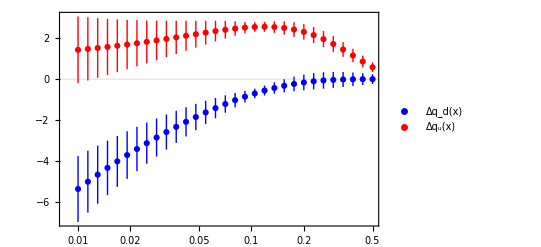

```mathematica
plt1=ListLogLinearPlot[{dVpol,uVpol},PlotTheme->"Scientific",PlotStyle->{Blue,Red},PlotRange->All,ImageSize->Scaled[0.2],PlotLegends->Placed[PointLegend[{Blue,Red},{"Δq_d(x)","Δq_u(x)"}],{0.8,0.3}]]
```

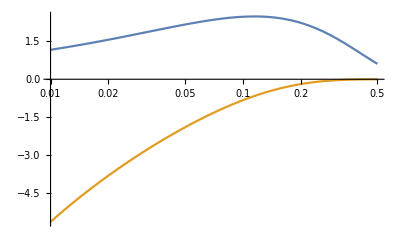

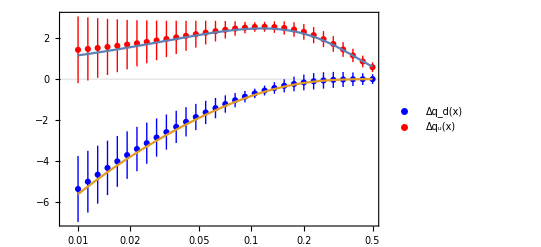

```mathematica
plt2= LogLinearPlot[{faz/.{n->11,α->-0.48,β->3.7},faz/.{n->-0.9,α->0.42,β->10}},{x,0.01,0.5}]
Show[plt1,plt2]
```

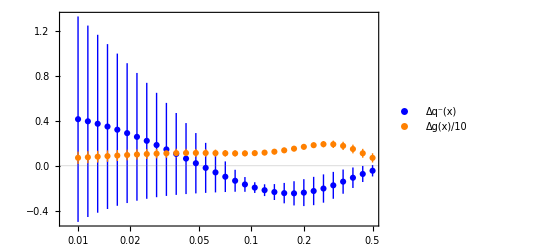

```mathematica
plt3=ListLogLinearPlot[{dbarpol,gpol},PlotTheme->"Scientific",PlotStyle->{Blue,Orange},PlotRange->All,ImageSize->Scaled[0.2],PlotLegends->Placed[PointLegend[{Blue,Orange},{"Δq^-(x)","Δg(x)/10"}],{0.8,0.8}]]
```

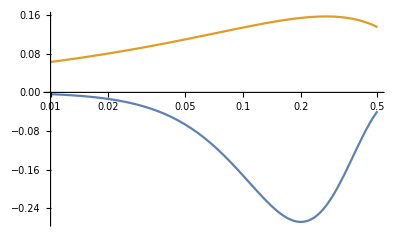

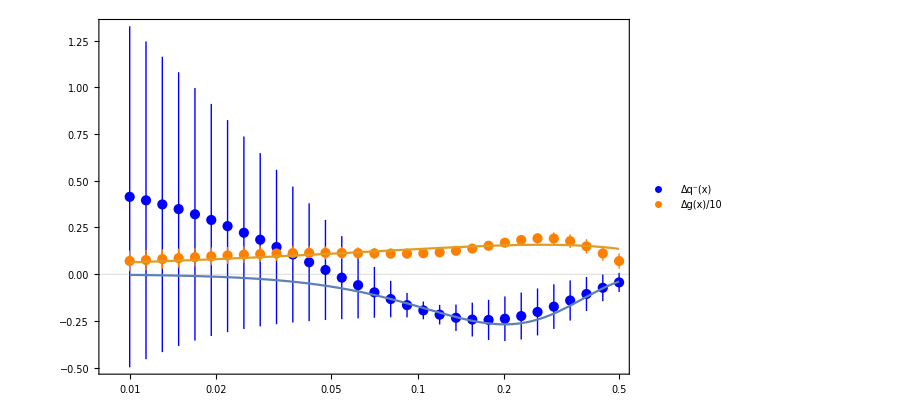

```mathematica
plt4= LogLinearPlot[{faz/.{n->-40,α->-2,β->8},faz/.{n->0.35,α->-0.37,β->1}},{x,0.01,0.5}]
Show[plt3,plt4]
```

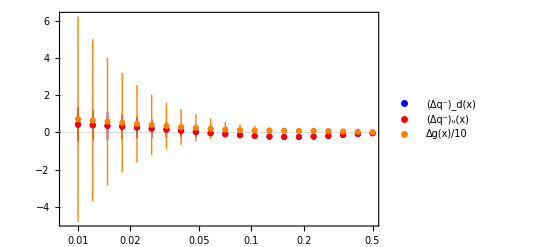

```mathematica
ListLogLinearPlot[{dbarpol,ubarpol,gpol},PlotTheme->"Scientific",PlotStyle->{Blue,Red,Orange},PlotRange->All,ImageSize->Scaled[0.2],PlotLegends->Placed[PointLegend[{Blue,Red,Orange},{"(Δq^-)_d(x)","(Δq^-)_u(x)","Δg(x)/10"}],{0.8,0.8}]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["./PDFDATA/dV_Unp.csv",{#[[1]],#[[2,1]],#[[2,2]]}& /@dVunp]
Export["./PDFDATA/uV_Unp.csv",{#[[1]],#[[2,1]],#[[2,2]]}& /@uVunp]
Export["./PDFDATA/dbar_Unp.csv",{#[[1]],#[[2,1]],#[[2,2]]}& /@dbarunp]
Export["./PDFDATA/ubar_Unp.csv",{#[[1]],#[[2,1]],#[[2,2]]}& /@ubarunp]
Export["./PDFDATA/g_Unp.csv",{#[[1]],#[[2,1]],#[[2,2]]}& /@gunp]

Export["./PDFDATA/dV_Pol.csv",{#[[1]],#[[2,1]],#[[2,2]]}& /@dVpol]
Export["./PDFDATA/uV_Pol.csv",{#[[1]],#[[2,1]],#[[2,2]]}& /@uVpol]
Export["./PDFDATA/qbar_Pol.csv",{#[[1]],#[[2,1]],#[[2,2]]}& /@ubarpol]
Export["./PDFDATA/g_Pol.csv",{#[[1]],#[[2,1]],#[[2,2]]}& /@gpol]
```

/Volumes/GoogleDrive/我的云端硬盘/jam22polJets-main

./PDFDATA/dV_Unp.csv

./PDFDATA/uV_Unp.csv

./PDFDATA/dbar_Unp.csv

./PDFDATA/ubar_Unp.csv

./PDFDATA/g_Unp.csv

./PDFDATA/dV_Pol.csv

./PDFDATA/uV_Pol.csv

./PDFDATA/qbar_Pol.csv

./PDFDATA/g_Pol.csv